```mathematica
(*wipeAll[]*)
```

```mathematica
SetDirectory@NotebookDirectory[];
(*<<"Physica/MathUtils.wl"*)
```

```mathematica
$Assumptions=λ>0&&r0>0&&z0>z>0&&w>w0>0&&y>1&&1>z0limit>0&&z0>cutoff>0
```

λ>0&&r0>0&&z0>z>0&&w>w0>0&&y>1&&1>z0limit>0&&z0>cutoff>0

## Field Theory

### log Z Integral

See <https://bryango.github.io/resources/journal/1805.06286-KutasovEtAl-EntanglementBeyond.html#c-function>.

#### Some mathematics

```mathematica
∫Cosh[x]^2 ⅆx
∫Sinh[x]^2 ⅆx

Sinh[x](Sinh[x]-Cosh[x])//TrigToExp//Simplify
∫%ⅆx
```

x/2+1/4 Sinh[2 x]

-x/2+1/4 Sinh[2 x]

1/2 (-1+ⅇ^(-2 x))

1/2 (-1/2 ⅇ^(-2 x)-x)

```mathematica
Assuming[lx>1,
exp=Exp[-2ArcCosh[lx]]//TrigToExp//Simplify;
exp//Print;

helperFactor=(lx-√(lx^2-1))^2;
Simplify[exp/helperFactor]*helperFactor//Expand//Print;
]
```

1/((lx+√(-1+lx^2))^2)

-1+2 lx^2-2 lx √(-1+lx^2)

#### Entropy & C-function

```mathematica
Assuming[lx>l0>0&&l0^2==(c*λs)/3,
logZ=c/3 ArcCosh[lx/l0]+lx^2/λs(1-√(1-(l0/lx)^2));

entropy=logZ-lx/2 D[logZ, lx]//Simplify;
cFunction=lx*D[entropy, lx]//Simplify;
]
Column[{
entropy,cFunction
}]
```

1/3 c ArcCosh[lx/l0]
(c lx)/(3 √(-l0^2+lx^2))

## Bulk RT

### Poincare Metric

```mathematica
(Dt[r]^2/(4 r^2)+(r*Dt[u]*Dt[v])/(1+2λ*r)/.r->1/z^2//FullSimplify)/.Dt[λ]->0
```

(Dt[u] Dt[v])/(z^2+2 λ)+Dt[z]^2/z^2

### Solving for the Geodesic

```mathematica
Remove[p]
dFactor=dilatonFactor=((z^2+2λ)/z^2)^2;
ϕdot=x/.Solve[p==dFactor*1/(z^2+2λ)*x,x]//First

zdot2=zdotSquared=x/.Solve[
dFactor*(x/z^2+ϕdot^2/(z^2+2λ))==1
,x
]//First//Simplify
```

(p z^4)/(z^2+2 λ)

(z^8-p^2 z^10+2 z^6 λ)/((z^2+2 λ)^3)

```mathematica
zdot2/ϕdot^2//Simplify

%-(1/(p^2 z^2)-z^2/(2 λ+z^2))//Simplify
```

(z^2-p^2 z^4+2 λ)/(p^2 z^2 (z^2+2 λ))

0

```mathematica
Solve[1/(p2 z^2)-z^2/(2 λ+z^2)==0,p2]/.z->z0
```

{{p2→(z0^2+2 λ)/z0^4}}

### Geodesic

```mathematica
geodesicEq=((zfunc'[phi])^2==z0^2/z^2 z0^2/(z0^2+2 λ)-z^2/(z^2+2 λ));
geodesicEq=geodesicEq/.{zfunc'[phi]->1/phi'[z]};
geodesicEq=Distribute[1/geodesicEq,Equal]//Simplify
(*Assuming[z0>z>0,
(*∫_z0^0 -√(%⟦2⟧)ⅆz*)
∫-√(%⟦2⟧)ⅆz//Simplify
]*)
```

phi'[z]^2==1/(-z^2/(z^2+2 λ)+z0^4/(z^2 (z0^2+2 λ)))

```mathematica
ClearAll[phi];

DSolve[{
geodesicEq,
phi[z0]==0
},
phi[z],
z
]//Simplify

(* "# Two branches of √x"; *)
(phi[z]/.First[%])+(phi[z]/.Last[%])==0

phi[z_]:=phi[z]/.Last[%%]//Evaluate;

"# Check solution";
geodesicEq//Simplify
```

{{phi[z]→-(2 ⅈ λ (EllipticE[ArcSin[√((z^2+2 λ)/(z0^2+2 λ))],((z0^2+2 λ)^2)/(4 λ^2)]-EllipticF[ArcSin[√((z^2+2 λ)/(z0^2+2 λ))],((z0^2+2 λ)^2)/(4 λ^2)]))/(√(z0^2+2 λ))},{phi[z]→(2 ⅈ λ (EllipticE[ArcSin[√((z^2+2 λ)/(z0^2+2 λ))],((z0^2+2 λ)^2)/(4 λ^2)]-EllipticF[ArcSin[√((z^2+2 λ)/(z0^2+2 λ))],((z0^2+2 λ)^2)/(4 λ^2)]))/(√(z0^2+2 λ))}}

True

True

```mathematica
ϕ[z_]:=(phi[z]-phi[z0])//Simplify//Evaluate;
ϕ[z]
```

-(2 ⅈ λ (EllipticE[((z0^2+2 λ)^2)/(4 λ^2)]-EllipticE[ArcSin[√((z^2+2 λ)/(z0^2+2 λ))],((z0^2+2 λ)^2)/(4 λ^2)]+EllipticF[ArcSin[√((z^2+2 λ)/(z0^2+2 λ))],((z0^2+2 λ)^2)/(4 λ^2)]-EllipticK[((z0^2+2 λ)^2)/(4 λ^2)]))/(√(z0^2+2 λ))

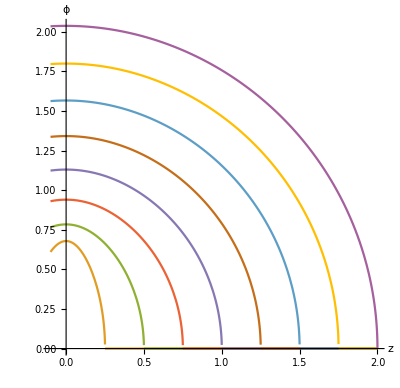

```mathematica
Block[{λ=1/3},
Plot[
Table[
ϕ[z]//Re,
{z0,$MachineEpsilon,2+$MachineEpsilon,.25}
]//Evaluate,
{z,-.1,2}
,PlotRange->Automatic
,AxesLabel->{"z","ϕ"}
,AspectRatio->Automatic
,PlotPoints->150
]
]
```

Alternative parameterization: w=1/z∝U (in Kutasov et al’s convention).

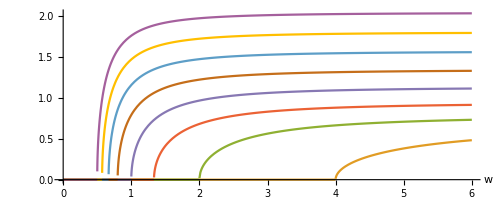

```mathematica
Block[{λ=1/3},
Plot[
Table[
ϕ[1/w]//Re,
{z0,$MachineEpsilon,2+$MachineEpsilon,.25}
]//Evaluate,
{w,0,6}
,PlotRange->Automatic
,AxesLabel->Automatic
,AspectRatio->Automatic
,PlotPoints->150
]
]
```

### Minimal Boundary Length L

```mathematica
(*
l$hold[w0_,λ_:1/2]:=Hold[2/w0∫_1^∞ (√(1+2λ*w0^2 y^2))/(y^2 √(y^2(1+2λ*w0^2 y^2)/(1+2λ*w0^2)-1))ⅆy];
l$numeric[w0_,λ_:1./2]:=l$hold[w0,λ]/.Integrate->NIntegrate//ReleaseHold;
*)
```

```mathematica
Assuming[a>0,
∫_1^∞ 1/(y √(y^4-1))ⅆy
]
```

π/4

```mathematica
l[z0_,λ_:1/2]:=2ϕ[0]//Evaluate;
```

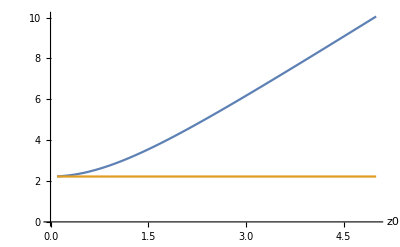

```mathematica
Block[{λ=1},
Plot[{
l[z0,λ]//Re,
√(λ/2)π
},
{z0,.1,5}
,PlotRange->{0,Automatic}
,AxesLabel->Automatic
]
]
```

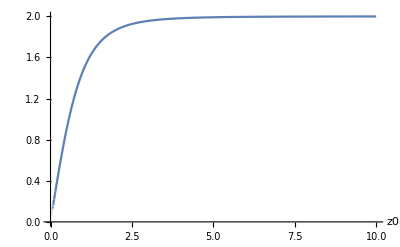

```mathematica
Plot[
D[l[z0], z0]//Evaluate,
{z0,0,10}
,PlotRange->{0,Automatic}
,MaxRecursion->10
,AxesLabel->Automatic
]
```

### Entropy (Area) (Geodesic Length)

Note: cutoff must be z_0 independent! From now on we take G_N=1.

```mathematica
1/2∫(z^2+2λ)/z^2 √(1/z^2+1/(z^2+2λ)/(z0^2/z^2 z0^2/(z0^2+2 λ)-z^2/(z^2+2 λ)))ⅆz//Simplify
s$indef$complex[z0_,z_,λ_:1/2]:=%//Evaluate;

"# Discard the Im part as it must be canceled";
s$indef$real[z0_,z_,λ_:1/2]:=s$indef$complex[z0,z,λ]//Re//Simplify//Evaluate;
```

((z^2-z0^2) (z^2+2 λ) (2 z0^2 λ+z^2 (z0^2+2 λ))-1/(((z^2+2 λ) (z0^2+2 λ))^(3/2))z0 (z^3+2 z λ)^2 (-2 z0^3 √((z^2-z0^2) (z0^2+2 λ) (2 z0^2 λ+z^2 (z0^2+2 λ))) EllipticF[ArcSin[(√((z^2+2 λ) (z0^2+2 λ)))/(2 λ)],(4 λ^2)/((z0^2+2 λ)^2)]+2 λ √(((z^2-z0^2) (z0^2+2 λ) (2 z0^2 λ+z^2 (z0^2+2 λ)))/(z0^2+4 λ)) ((z0^2+4 λ) EllipticE[ArcSin[1/2 √(-(2 z0^2 λ+z^2 (z0^2+2 λ))/λ^2)],-(4 λ^2)/(z0^4+4 z0^2 λ)]-(z0^2+2 λ) EllipticF[ArcSin[1/2 √(-(2 z0^2 λ+z^2 (z0^2+2 λ))/λ^2)],-(4 λ^2)/(z0^4+4 z0^2 λ)])+z0^3 λ √(((z^2-z0^2) (z0^2+2 λ) (2 z0^2 λ+z^2 (z0^2+2 λ)))/(z0^2 λ^2 (z0^2+4 λ))) ((z0^2+4 λ) EllipticE[ArcSin[1/2 √(-(2 z0^2 λ+z^2 (z0^2+2 λ))/λ^2)],-(4 λ^2)/(z0^4+4 z0^2 λ)]-(z0^2+2 λ) EllipticF[ArcSin[1/2 √(-(2 z0^2 λ+z^2 (z0^2+2 λ))/λ^2)],-(4 λ^2)/(z0^4+4 z0^2 λ)])+2 z0^3 √((z^2-z0^2) (z0^2+2 λ) (2 z0^2 λ+z^2 (z0^2+2 λ))) EllipticPi[(2 λ)/(z0^2+2 λ),ArcSin[(√((z^2+2 λ) (z0^2+2 λ)))/(2 λ)],(4 λ^2)/((z0^2+2 λ)^2)]))/(4 z z0^2 √((z^2+2 λ) (z^4 z0^4+2 z^2 z0^4 λ-z^6 (z0^2+2 λ))))

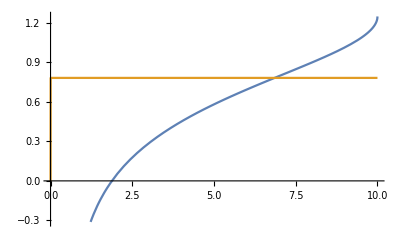

```mathematica
Plot[
s$indef$complex[10,z]//ReIm//Evaluate,
{z,0,10}
]
```

```mathematica
s$indef$z0experiment=Parallelize[
Limit[s$indef$complex[#,z],z->10,Direction->"FromBelow"]&/@Range[1,10]
]
```

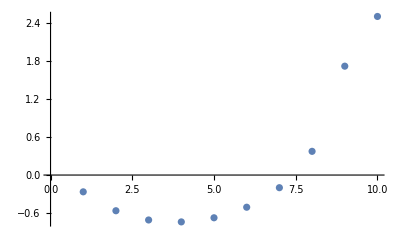

```mathematica
s$indef$z0experiment=;
s$indef$z0experiment//Re//N//ListPlot
```

```mathematica
D[(s$indef$complex[z0,(1-10^-7)z0]-s$indef$complex[z0,.0001]), z0]//ReIm;

Plot[
%//Evaluate,
{z0,0,1}
,PlotRange->{0,10}
,PlotLabels->{"Re","Im"}
]
```

-Graphics-

```mathematica
ds[z0_,λ_:1/2,z0limit_:1-10^-7,cutoff_:.0001]=(
D[(s$indef$complex[z0,z0limit*z0]-s$indef$complex[z0,cutoff]), z0]
)//Evaluate;
```

```mathematica
Plot[
ds[z0]//ReIm//Evaluate,
{z0,0,1}
,PlotRange->{0,10}
,PlotLabels->{"Re","Im"}
]
```

-Graphics-

The numerical stability is questionable! Needs to be careful.

```mathematica
c[z0_,λ_:1/2,z0limit_:1-10^-7,cutoff_:.0001]=(
l[z0,λ]*ds[z0,λ,z0limit,cutoff]/D[l[z0,λ], z0]
)//Re//Evaluate;
```

c=(3l)/(2 G_N)=6k p

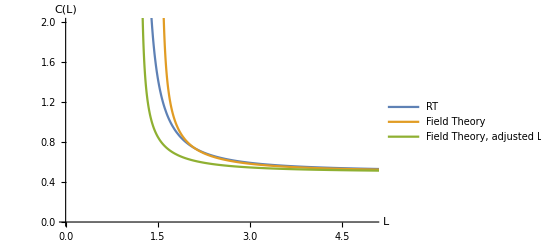

```mathematica
ParametricPlot[{
{l[x,λ],c[x,λ,1-10^-7,.0001]},
{x,(1/2)/(√(1-(√(8λ))^2/x^2))},
{x,(1/2)/(√(1-(√(λ/2)π)^2/x^2))}
}/.{λ->.3}//Evaluate
,{x,0,10}
,PlotRange->{{0,5},{0,2}}
,AspectRatio->1/GoldenRatio
,PlotLegends->{
"RT"
,"Field Theory"
,"Field Theory, adjusted L_min"
}
,AxesLabel->{"L","C(L)"}
]
```

### Match with Kutasov et al

```mathematica
(*(z^2+2λ)/z^2 Dt[z] √(1/z^2+1/(z^2+2λ)/(z0^2/z^2 z0^2/(z0^2+2 λ)-z^2/(z^2+2 λ)))/.{z->1/w,z0->1/w0}//FullSimplify*)
```

```mathematica
1/((w^4+2 w^6 λ)/(w^2-w0^2+2 w^4 λ-2 w0^4 λ)*1/w^2)-1//FullSimplify
```

-(w0^2+2 w0^4 λ)/(w^2+2 w^4 λ)

```mathematica
(Dt[r]^2/(4 r^2)+(r*Dt[u]*Dt[v])/(1+2λ*r)/.r->w^2//FullSimplify)/.Dt[λ]->0
```

(w^2 Dt[u] Dt[v])/(1+2 w^2 λ)+Dt[w]^2/w^2

```mathematica
∫(1+2λ*w0^2 y^2)/(y √(1-1/y^2(1+2λ*w0^2)/(1+2λ*w0^2 y^2)))ⅆy
```

∫(1+2 w0^2 y^2 λ)/(y √(1-(1+2 w0^2 λ)/(y^2 (1+2 w0^2 y^2 λ))))ⅆy

### More